Instructions on how to download the SXS database and configure it with Mathematica are at:
https://sxs.readthedocs.io/en/main/#installation
https://sxs.readthedocs.io/en/main/mathematica/

```mathematica
ClearAll["Global`*"];Off[General::spell];Remove["Global`*"]
SetOptions[Simplify,TimeConstraint->1000];
$MinPrecision=$MachinePrecision;
```

```mathematica
session=StartExternalSession[<|"System"->"Python","Executable"->"/usr/local/anaconda3/bin/python"|>];
py=ExternalEvaluate[session];
```

SetPrecision::precsm: Requested precision 5 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of SetPrecision::precsm will be suppressed during this calculation.

```mathematica
py["import sxs"];
```

```mathematica
py["catalog = sxs.load('catalog')"]
```

Skipping download from 'https://data.black-holes.org/catalog.json' because local file is newer

```mathematica
sims=py["catalog.table"];
```

Found the following files to load from the SXS catalog:

SXS:BBH:0180v5/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5

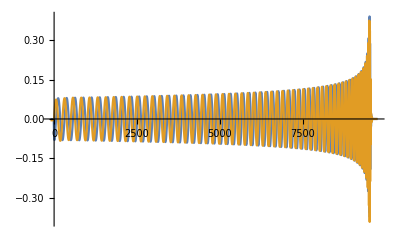

```mathematica
py["wBBH0180 = sxs.load('SXS:BBH:0180/Lev/rhOverM', extrapolation_order=4)"]
tBBH0180=Normal[py["wBBH0180.time"]];
m22BBH0180=Normal[py["wBBH0180.data[:, wBBH0180.index(2, 2)]"]];
ListLinePlot[{Transpose[{tBBH0180,Re[m22BBH0180]}],Transpose[{tBBH0180,Im[m22BBH0180]}]}]
```

Found the following files to load from the SXS catalog:

SXS:BBH:0746v5/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5

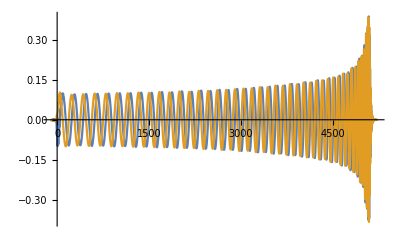

```mathematica
py["wBBH0746 = sxs.load('SXS:BBH:0746/Lev/rhOverM', extrapolation_order=4)"]
tBBH0746=Normal[py["wBBH0746.time"]];
m22BBH0746=Normal[py["wBBH0746.data[:, wBBH0746.index(2, 2)]"]];
ListLinePlot[{Transpose[{tBBH0746,Re[m22BBH0746]}],Transpose[{tBBH0746,Im[m22BBH0746]}]}]
```

```mathematica
BBH0180Table = Transpose[{tBBH0180,Re[m22BBH0180], Im[m22BBH0180]}];
```

```mathematica
Export["BBH0180_22.dat",BBH0180Table,"Table"]
```

BBH0180_22.dat

```mathematica
BBH0746Table = Transpose[{tBBH0746,Re[m22BBH0746], Im[m22BBH0746]}];
```

```mathematica
Export["BBH0746_22.dat",BBH0746Table,"Table"]
```

BBH0746_22.dat

```mathematica
sBBH0180=Normal[py["wBBH0180.evaluate(0.0, 0.0)"]]  (*(θ,ϕ)=(0.1,0.2)*)
```

{-0.000278678-0.00297437 ⅈ,-0.000279991-0.00298318 ⅈ,-0.000281328-0.00299188 ⅈ,19290,-5.25554×10^-6-0.0000124291 ⅈ,-5.26213×10^-6-0.0000124275 ⅈ}
 |  |  |  |

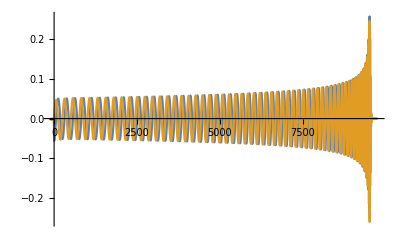

```mathematica
ListLinePlot[{Transpose[{tBBH0180,Re[sBBH0180]}],Transpose[{tBBH0180,Im[sBBH0180]}]}]
```

```mathematica
Export["BBH0180_h.dat",Transpose[{tBBH0180,Re[sBBH0180], Im[sBBH0180]}],"Table"]
```

BBH0180_h.dat